FittedModel[554.618/(1+42.9926 ⅇ^(-0.538518 x))]

{554.618/(1+42.9926 ⅇ^(-0.538518 x)), | Estimate | Standard Error | t-Statistic | P-Value
a | 42.9926 | 4.63188 | 9.2819 | 7.58938×10^-11
b | 0.538518 | 0.0151647 | 35.5114 | 1.83947×10^-28
c | 554.618 | 1.96449 | 282.322 | 6.91448×10^-59}

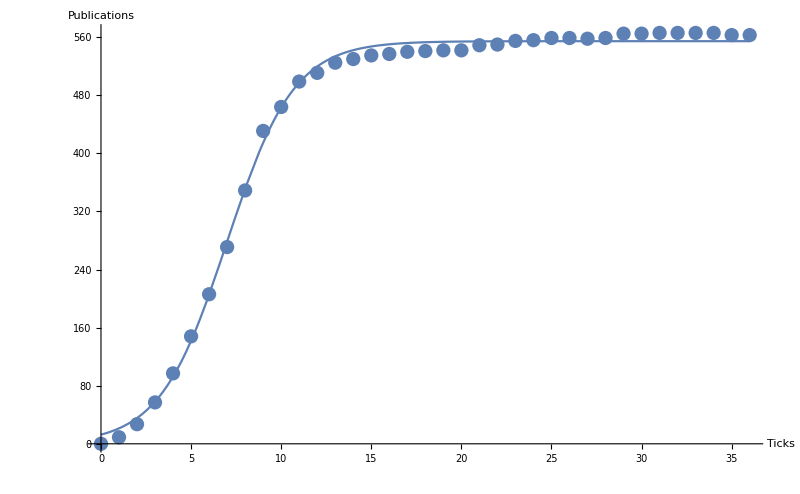

```mathematica
dataPublicationsCurve = Import["/home/fabianact/Tesis/Pruebas/ModelGrid/testTables/publicationstest-curve.csv"];
fitFkt=NonlinearModelFit[dataPublicationsCurve,c/(1+a Exp[-b x]),{a,b,c},x]
fitFkt[{"BestFit","ParameterTable"}]
plot=Show[ListPlot[dataPublicationsCurve,ImageSize->800,AxesLabel->{"Ticks","Publications"}],Plot[fitFkt[x],{x,0,36}]]
Export["fit.png",plot];
```